# Charge, Phase and Flux Artificial Atom Qubits

In Notebook 8.3 we investigated the energy level structure of an isolated Josephson junction (JJ), the building block of artificial atom qubits in the superconducting circuit paradigm. The latter are usually divided into three classes which we discuss below.

## Charge Qubits

In a typical charge qubit, the Cooper pair box (CPB), a superconducting element one one side of the JJ is shunted by a capacitor as shown in the figures below

In the top figure a superconducting island is sandwiched between a JJ (on its right) and a gate capacitor C_gon its left. The bottom figure is an equivalent lumped circuit representation of that set-up.
Because of the presence of the gate capacitor, in addition to the intrinsic capacitance of the junction, the charging energy term given in Notebook8.3 is modified so that

and since

We obtain the Schrodinger equation

We  define a gauge transformation

and obtain a Schrodinger equation

which has the same form as the equation studied in Notebook8.3, and whose solutions are expressed in terms of Mathieu functions. 
Let ϕ= θ/2 , a=ϵ-γ', q ≡ -γ'/2, and  we get the Mathieu equation for f(ϕ)

whose general solution is

f(ϕ)=c_1MathieuC[a,q,ϕ] + c_2 MathieuS[a,q,ϕ]

or

ψ(θ)=c_1exp(-i A_g θ)  MathieuC[a,q,θ/2] + c_2 exp(-i A_g θ)  MathieuS[a,q,θ/2]

According to the Floquet theorem the Mathieu functions have the property

M(a,q,θ/2+ n θ) = M(a,q,θ/2) e^(i π n r)

where n is an integer and  r is the characteristic exponent for a given value of a, Therefore

ψ(θ+2 π n ) = c_1exp(-i A_g θ)  exp(-i 2 π n A_g )MathieuC[a,q,θ/2]e^(i π n r) + c_2exp(-i A_g θ)  exp(-i 2 π n A_g )MathieuS[a,q,θ/2]e^(i π n r)  = exp(-2 π i  n A_g θ)  e^(i π n r) ψ(θ )

Since we require adherence to the boundary condition

exp(-π i n  (2 A_g-r)) =1   or   2 A_g-r    is an even integer

Let’s investigate the nature of these solution for the cases where
A_g = 0, 1, 2, ...
In that case we require that r, the characteristic exponent, is an even integer. By finding the values of a= ϵ-γ'  for which r=0,2,4,... we find the energy spectrum obtained in Notebook8.3.
However, for other values of A_g the energy spectrum is modified. For example,  let’s assume that  A_g=1/2 and q=-1/2  (γ'= 1).

For the class of solutions in which c_2=0, we require that r=1,3.... For the ground state r=1, we need to find

```mathematica
q=-1/2;
Ag=1/2;
a0=N[MathieuCharacteristicA[-1,q]]
```

0.470654

{Re[ⅇ^(-(ⅈ θ)/2) MathieuC[0.470654,-1/2,θ/2]],Im[ⅇ^(-(ⅈ θ)/2) MathieuC[0.470654,-1/2,θ/2]]}

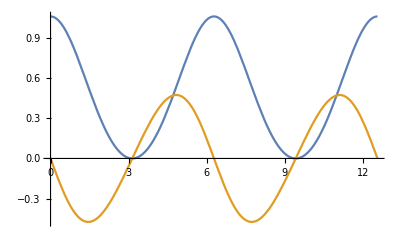

```mathematica
wave1={Re[Exp[-I Ag θ]MathieuC[a0,q,θ/2]],Im[Exp[-I Ag θ]MathieuC[a0,q,θ/2]]}
Plot[wave1,{θ,0,4Pi}]
```

Note that ψ(θ) does indeed satisfy boundary condition (2). The energy eigenvalue is given by

ϵ= a +γ'= a0 - 2 q  = 0.4706+1.0= 1.4706

Consider now the case given in Notebook 8.3 and in which A_g= 0, or r =0,2 ...

```mathematica
q=-1/2;
Ag=0;
a1=N[MathieuCharacteristicA[0,q]]
```

-0.121766

{Re[MathieuC[-0.121766,-1/2,θ/2]],Im[MathieuC[-0.121766,-1/2,θ/2]]}

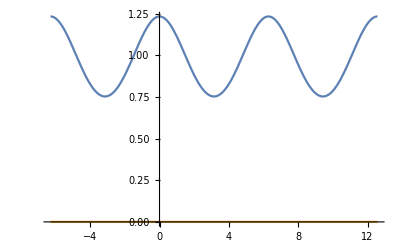

```mathematica
wave2={Re[Exp[-I Ag θ]MathieuC[a1,q,θ/2]],Im[Exp[-I Ag θ]MathieuC[a1,q,θ/2]]}
Plot[wave2,{θ,-2Pi,4Pi}]
```

Again, this ground state wavefunction obeys the boundary condition (2), but has energy eigenvalue

ϵ = a1 -2 q = -0.121766+ 1 = 0.87823

Thus with the Copper Pair Box (CPB) charge qubit one can tune the energy eigenvalues of the artificial atom by adjusting the voltage V_g. The CPB was introduced in order to tame fluctuations of residual offset charge in a bare JJ.

### Relation to the Aharonov - Bohm Effect

The term A_g introduced above has a very interesting analogue, called the Aharonov-Bohm effect. Consider a charged particle that is constrained to move on a circular 2D track (i.e. a rotor) as shown below. In addition, this track is threaded by a magnetic flux tube (i.e. the magnetic field is non-zero only inside the tube and is directed along the tube axis).

The presence of magnetic flux allows the charged particle to minimally couple to a vector potential. The latter leads to observable effects, such as a modification in the rotor’s energy level spectrum. 
For this system, the resulting kinetic energy component of the Hamiltonian has a structure similar to  that described by Eq. (1). Today, it is know that few-body systems (atoms, molecules etc. ) also posses similar gauge structures, and which, lead to interesting dynamical and topological effects.

## Phase Qubits

In a phase qubit the JJ is current biased.  The circuit diagram for a phase qubit is

The fixed DC-current source introduces an additional term - I_0Φ ,where I_0is a constant, to the Hamiltonian given in Notebook8.3. Its inclusion modifies the periodic potential

E_J (1- Cos(Φ/Φ_0) )⟶  E_J (1- Cos(Φ/Φ_0) ) -  I_0 Φ

Or,

```mathematica
v[θ_,γ_,χ_]=γ(1-Cos[θ])-χ θ;
```

θ=ϕ/ϕ_0, γ=E_J/E_(C,)  χ= I_0ϕ_0/E_C,

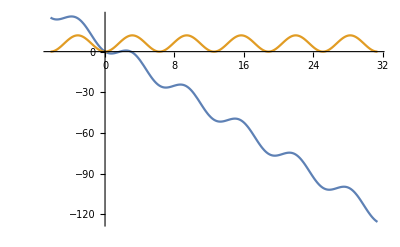

```mathematica
(* Here we plot the potentials for the values γ=6, χ=1 (blue line), and γ=6, χ=0 (beige line)*)
Plot[{v[θ,6,4],v[θ,6,0]},{θ,-2Pi,10Pi}]
```

The beige line represents the potential, as a function of θ, for the case χ=0 (i.e a charge qubit potential). The blue line represents the potential for the case χ=1. Because of its downward slope, it is called a tilted “washboard” potential. In the vicinity θ=0, the energy eigenstates are unstable as they can “tunnel” through the barrier on the right. The ground state whose energy eigenvalue is shown by the red line in the figure below could have a relatively long lifetime as the tunneling probability is small, however the dotted line represents a state that has a much shorter lifetime due to its enhanced ability to tunnel at the rightmost barrier.

One important feature of the phase qubit is that it allows readout capabilities. Suppose the system occupies the ground state. An excitation of it populates an excited, short-lived, state shown by the dotted line. In that state, phase quanta can tunnel through the barrier and accelerate down the washboard. That motion produces a voltage that allows detection. By tuning the value of the external current I_0 one can adjust the tunneling probability of the quasi-bound states.

## Flux Qubits

In a flux qubit the JJ is by inductively coupled to a constant current source as shown in the circuit below.

The superconducting circuit on the left generates a magnetic field which induces an external flux Φ_e in the circuit containing the JJ on the right. In the superconducting circuit on the right,  a persistent current, due to the magnetic flux contained by the circuit, is induced. If L is the self-inductance of that circuit, I the persistent current, and ϕ the generalized flux coordinate, then

L I = ϕ- ϕ_e

As the energy stored by an inductor is given by the expression

1/2 L I^2 = (ϕ-ϕ_e)^2/2L

Hamiltonian Eq. (8.56) in the text is modified to

H= E_C (Q/e)^2 + E_J(1- Cos(ϕ/ϕ_0) )+ (ϕ-ϕ_e)^2/2L

It is useful to define the coordinate χ= ϕ - ϕ_e and so

H= E_C (Q/e)^2 + E_J(1- Cos( χ/ϕ_0 + ϕ_e/ϕ_0) )+ χ^2/2L

In the Schrodinger equation the effective potential now has the form

V(θ)= γ(1-  Cos (θ +  θ_e ))+ β θ^2

where θ=χ/ϕ_0, γ = E_J/E_C, θ_e=ϕ_e/ϕ_o and β=ϕ_0^2/2 L E_C

```mathematica
vf[θ_,γ_,β_,θe_]=γ(1- Cos[θ+θe])+ β θ^2
```

β θ^2+γ (1-Cos[θ+θe])

Lets expand this potential about θ ≈ 0

```mathematica
FullSimplify[Normal[Series[vf[θ,γ,β,θe],{θ,0,4}]]]
```

γ+β θ^2-1/24 γ (24-12 θ^2+θ^4) Cos[θe]-1/6 γ θ (-6+θ^2) Sin[θe]

If we set the external flux θ_e to values that are integral odd multiples of π  the potential (3) takes the form of a double well.  For example,

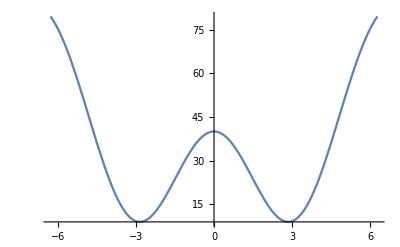

```mathematica
Plot[vf[θ,20,1.0,Pi],{θ,-2Pi,2Pi}]
```

Typically the eigenstates of  a double well potential contains an almost degenerate pair of ground states shown the red lines in the figure below

These two states would truly be degenerate if the barrier at θ≃0 does not allow quantum tunneling. However for sufficiently narrow barriers, tunneling splits the levels into two non-degenerate states separated by a narrow energy gap Δ. They play the role of the qubit computational basis |0⟩, |1⟩.